# Mutation distribution fitting

```mathematica
(* Global configuration*)
export = True; (* True to export images *)
On[Assert];
```

## Data input

## Set working directory

```mathematica
SetDirectory[NotebookDirectory[]<>"results"]
```

/mnt/Ad115/Programming/ICGC-data-parser/workflows-&-examples/mutations-per-gene/results

## Import data

```mathematica
FileNames[]
```

{gene-mutations-all.out,gene-mutations-BRCA-EU.out}

```mathematica
data = Import["gene-mutations-BRCA-EU.out"]; 
(* Tests *)
data[[;;2]]
data[[-10;;]]
```

{{():,1902358},{CNTNAP2(ENSG00000174469):,4963}}

{{AC010877.1(ENSG00000269291):,1},{UTY(ENSG00000183878):,1},{HDHD1P1(ENSG00000234620):,1},{ZFY(ENSG00000067646):,1},{PPP1R12BP1(ENSG00000229238):,1},{TPTE2P4(ENSG00000215506):,1},{CYCSP49(ENSG00000224240):,1},{RNF19BPY(ENSG00000225653):,1},{TSPY11P(ENSG00000238235):,1},{FAM197Y9(ENSG00000234830):,1}}

## Structure data as a Dataset

```mathematica
(*Get cancer project*)
project = "BRCA-EU"

(*Get column headers*)
headers = {"GENE SYMBOL", "GENE ID", "MUTATIONS"}
```

BRCA-EU

{GENE SYMBOL,GENE ID,MUTATIONS}

```mathematica
(*Split a gene string of the form "NAME(GENE_ID):" into NAME and GENE_ID parts.*)
SplitGene = StringCases[#, 
					{StartOfString~~x__~~"("-> x,  (* Match the NAME part *)
					"("~~x__~~")"                       -> x},(* Match the GENE_ID part *)
					Overlaps->True]&;
```

```mathematica
(*Splits a line from the data into items.
A line from the imported data has the form: 
		{ "GENE_NAME(GENE_ID):", MUTATIONS }
*)
DataItems[{geneStr_, mutations_}] := Module[{splitted, genePart},
splitted =SplitGene[geneStr] ;
(* Handle the case of no affected genes*)
genePart = If[splitted≠{}, 
			splitted, 
			{"", ""}];
Return[ Append[genePart, mutations] ]
]
(* Tests *)
lines = data⟦;;3⟧
Map[DataItems,lines]
```

{{():,1902358},{CNTNAP2(ENSG00000174469):,4963},{LSAMP(ENSG00000185565):,4501}}

{{,,1902358},{CNTNAP2,ENSG00000174469,4963},{LSAMP,ENSG00000185565,4501}}

```mathematica
(* Convert items from the imported data to an association apt for being added to a dataset. *)
ItemsToAssociation[lineitems_ , headers_] := Module[{mapped},
(* Map names to items *)
mapped = Table[ <|headers[[i]]->lineitems[[i]]|>, {i, Length[headers]}];
(* Convert to association *)
Return[ Association[mapped] ]
]

(*Convert lines from the imported data to an association apt for being added to a dataset.*)
LineToAssociation[headers_, line_] := ItemsToAssociation[DataItems[line], headers]
LineToAssociation[headers_]:= LineToAssociation[headers, #]&

(* Test the new functions *)
lines = data⟦;;3⟧
Map[LineToAssociation[headers], lines]
```

{{():,1902358},{CNTNAP2(ENSG00000174469):,4963},{LSAMP(ENSG00000185565):,4501}}

{<|GENE SYMBOL→,GENE ID→,MUTATIONS→1902358|>,<|GENE SYMBOL→CNTNAP2,GENE ID→ENSG00000174469,MUTATIONS→4963|>,<|GENE SYMBOL→LSAMP,GENE ID→ENSG00000185565,MUTATIONS→4501|>}

```mathematica
(* Convert the imported data to a dataset *)
dataset = Dataset[ LineToAssociation[headers] /@ data ]
(*Some tests*)
dataset[500]
data⟦500⟧
dataset[Total,"MUTATIONS"]
Total[ (#⟦2⟧)& /@ data]
dataset[Select[#⟦"GENE SYMBOL"⟧=="TP53"&]]
```

Dataset[<>]

Dataset[<>]

{COL19A1(ENSG00000082293):,603}

4878783

4878783

Dataset[<>]

```mathematica
(* Alternate way to make a query to the dataset. *)
SelectRow[selectFunc_, dataset_]:= dataset[Select[selectFunc]]
SelectRow[selectFunc_]:=SelectRow[selectFunc, #]&
(* Test *)
SelectRow[#⟦"GENE SYMBOL"⟧ == "TP53"&, dataset]
dataset[Select[#⟦"GENE SYMBOL"⟧ == "TP53"&]]
```

Dataset[<>]

Dataset[<>]

## Main genes localization

Now, we specify the main subsets of genes we are interested in

```mathematica
(* The main 6 genes in the Yau network *)
mainGenes6 = { "CDK2", "TP53", "MDM2","BRCA1","ERBB2", "ATM" }
(* The complete genes in the network *)
mainGenes16 = Join[ 
mainGenes6, 
{"AKT1","CHEK1","CHEK2","E2F1","ATR","HRAS","KRAS","NRAS","CDKN1A","RAF1"}
]
(* Extra genes to sample more data from the distribution *)
mainGenes20=Join[
mainGenes16,
{"LRP1B","RYR2","BRAF","KMT2C", "RB1"}
]
```

{CDK2,TP53,MDM2,BRCA1,ERBB2,ATM}

{CDK2,TP53,MDM2,BRCA1,ERBB2,ATM,AKT1,CHEK1,CHEK2,E2F1,ATR,HRAS,KRAS,NRAS,CDKN1A,RAF1}

{CDK2,TP53,MDM2,BRCA1,ERBB2,ATM,AKT1,CHEK1,CHEK2,E2F1,ATR,HRAS,KRAS,NRAS,CDKN1A,RAF1,LRP1B,RYR2,BRAF,KMT2C,RB1}

```mathematica
(* Select the rows in which the given genes appear. *)
FindGenes[genes_, dataset_]:=SelectRow[MemberQ[genes, #⟦"GENE SYMBOL"⟧]&, dataset]
(* Test *)
FindGenes[mainGenes16, dataset]
```

Dataset[<>]

```mathematica
(* Find specific data about a gene. *)
GeneLookup[dataset_, gene_, column_]:= ( (* Select the row that contains the gene *)
									     SelectRow[(#⟦"GENE SYMBOL"⟧== gene)∨(#⟦"GENE ID"⟧== gene)&,dataset]
									 (* A list of 1 element (the row as an association) is returned, get the item *)
									⟦1⟧
									    (* Get the specified column of the row *)
									  ⟦column⟧ )
(* Tests *)
GeneLookup[dataset, "TP53", "MUTATIONS"]
GeneLookup[dataset, "ENSG00000141510", "MUTATIONS"]
```

193

193

```mathematica
(* Search the mutations count for a gene. *)
GetMutations[gene_, dataset_] := {gene, GeneLookup[dataset, gene, "MUTATIONS"]}
GetMutations[dataset_]:=GetMutations[#, dataset]&
(* Test *)
GetMutations["TP53", dataset]
mainGenesHist = Map[GetMutations[dataset],mainGenes16]
```

{TP53,193}

{{CDK2,13},{TP53,193},{MDM2,83},{BRCA1,98},{ERBB2,119},{ATM,141},{AKT1,36},{CHEK1,51},{CHEK2,73},{E2F1,28},{ATR,194},{HRAS,20},{KRAS,54},{NRAS,26},{CDKN1A,25},{RAF1,84}}

{{CDK2,13},{TP53,193},{MDM2,83},{BRCA1,98},{ERBB2,119},{ATM,141},{AKT1,36},{CHEK1,51},{CHEK2,73},{E2F1,28},{ATR,194},{HRAS,20},{KRAS,54},{NRAS,26},{CDKN1A,25},{RAF1,84}}

{194ATR,193TP53,141ATM,119ERBB2,98BRCA1,84RAF1,83MDM2,73CHEK2,54KRAS,51CHEK1,36AKT1,28E2F1,26NRAS,25CDKN1A,20HRAS,13CDK2}

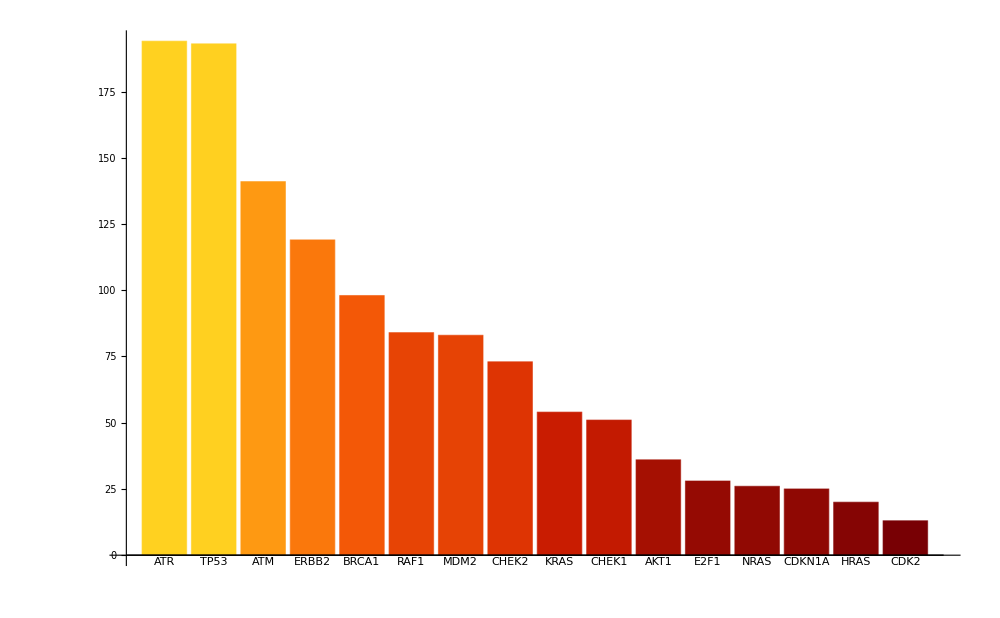

```mathematica
mainGenesHist = Map[GetMutations[dataset],mainGenes16]
mainGenesHist = Reverse[Sort[Apply[Labeled,Reverse[mainGenesHist,2],{1}]]]

bars = BarChart[mainGenesHist, ImageSize->1000, ColorFunction->ColorData["SolarColors"], BaseStyle->{FontFamily-> "ArialBlack"}]
```

```mathematica
If[export,
Export["./bars.svg", bars]
];
```

```mathematica
(* Fetch pairs {GENE, MUTATIONS} fot the top mutated genes. *)
GetTopMutated[dataset_,n_] := (dataset⟦All, {"GENE SYMBOL", "MUTATIONS"}⟧
				                                         (* Remove the case when no gene was affected *)
				                                         ⟦2;;⟧
				                                          (* Get the top n *)
				                                           ⟦;;n⟧)
(* Test *)
top100Mutated = GetTopMutated[dataset, 100]
```

Dataset[<>]

```mathematica
(* Check how many of the genes we are interested in are already there *)
FindGenes[mainGenes16, top100Mutated]
```

Dataset[<>]

```mathematica
(* So, we are not interested in the top 100, but in the top 100 - 16 = 84 *)
top84Mutated = GetTopMutated[dataset, 84]
```

Dataset[<>]

```mathematica
(* Also, we are interested in the top 50 - 16 = 34 *)
top34Mutated = GetTopMutated[dataset, 34]
```

Dataset[<>]

```mathematica
allMutated = MutationData[dataset]
```

{{,1902358},{CNTNAP2,4963},{LSAMP,4501},{RBFOX1,4223},{CSMD1,4175},{DMD,4132},{PTPRD,3791},{CTNNA2,3567},{PCDH15,3425},{EYS,3375},{RP11-420N3.2,3263},{MACROD2,3126},{CSMD3,3046},{LRP1B,2961},{DPP10,2945},{IL1RAPL1,2868},{ROBO2,2759},56847,{AC010970.1,1},{AC134878.2,1},{AC134878.1,1},{ASS1P6,1},{RPS24P1,1},{RN7SL702P,1},{SHROOM2P1,1},{AC010877.1,1},{UTY,1},{HDHD1P1,1},{ZFY,1},{PPP1R12BP1,1},{TPTE2P4,1},{CYCSP49,1},{RNF19BPY,1},{TSPY11P,1},{FAM197Y9,1}}
 |  |  |  |

```mathematica
(* Get data for a histogram of the genes. *)
MutationData[dataset_]:= Table[{dataset⟦i, "GENE SYMBOL"⟧, dataset⟦i, "MUTATIONS"⟧} , 
			                                   {i, Length[dataset]}]
(* Test *)
MutationData[top34Mutated]
```

{{CNTNAP2,4963},{LSAMP,4501},{RBFOX1,4223},{CSMD1,4175},{DMD,4132},{PTPRD,3791},{CTNNA2,3567},{PCDH15,3425},{EYS,3375},{RP11-420N3.2,3263},{MACROD2,3126},{CSMD3,3046},{LRP1B,2961},{DPP10,2945},{IL1RAPL1,2868},{ROBO2,2759},{DLG2,2728},{GPC5,2694},{CTNNA3,2555},{MAGI2,2525},{RP11-127H5.1,2459},{NRXN3,2371},{DPP6,2350},{OPCML,2291},{LRRC4C,2243},{AC007682.1,2235},{PARK2,2213},{DCC,2192},{SNTG1,2156},{TMEM132D,2108},{AGBL4,2101},{KCNIP4,2099},{NAALADL2,2083},{PTPRN2,2072}}

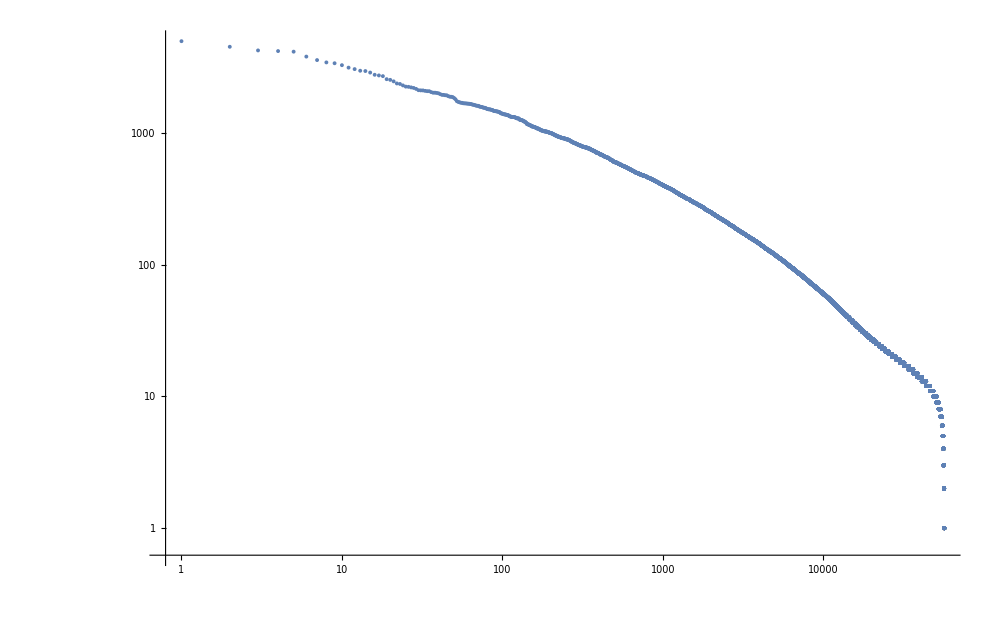

```mathematica
(* Plot mutation data *)
Options[MutationHistogram] = {Labeled->True, PlotFunction-> BarChart, ScalingFunctions-> None};
MutationHistogram[data_, OptionsPattern[]]:= Module[{preprocessedData,sortedData,plot},
(* Label data if asked to *)
preprocessedData = If[OptionValue[Labeled],
				        Apply[Labeled,Reverse[data,2],{1}],
				        Map[#⟦2⟧&,data]];
sortedData = Reverse[Sort[preprocessedData]];
OptionValue[PlotFunction][
		sortedData, 
		ScalingFunctions-> OptionValue[ScalingFunctions],
		ImageSize->1000, 
		ColorFunction->ColorData["SolarColors"], 
		BaseStyle->{FontFamily-> "ArialBlack"}]
]
(* Test *)
distribution = MutationHistogram[allMutated⟦2;;⟧, 
				  Labeled->False,
				  PlotFunction->ListPlot,
				    ScalingFunctions-> {"Log","Log"}]
```

```mathematica
If[export,
Export["./geneMutationsDistribution.svg", distribution];
];
```

```mathematica
important50 = Join[MutationData[top34Mutated], (* Top 34 mutated genes *)
				 Map[GetMutations[dataset],mainGenes16] (* Main 16 genes *)
]
```

{{CNTNAP2,4963},{LSAMP,4501},{RBFOX1,4223},{CSMD1,4175},{DMD,4132},{PTPRD,3791},{CTNNA2,3567},{PCDH15,3425},{EYS,3375},{RP11-420N3.2,3263},{MACROD2,3126},{CSMD3,3046},{LRP1B,2961},{DPP10,2945},{IL1RAPL1,2868},{ROBO2,2759},{DLG2,2728},{GPC5,2694},{CTNNA3,2555},{MAGI2,2525},{RP11-127H5.1,2459},{NRXN3,2371},{DPP6,2350},{OPCML,2291},{LRRC4C,2243},{AC007682.1,2235},{PARK2,2213},{DCC,2192},{SNTG1,2156},{TMEM132D,2108},{AGBL4,2101},{KCNIP4,2099},{NAALADL2,2083},{PTPRN2,2072},{CDK2,13},{TP53,193},{MDM2,83},{BRCA1,98},{ERBB2,119},{ATM,141},{AKT1,36},{CHEK1,51},{CHEK2,73},{E2F1,28},{ATR,194},{HRAS,20},{KRAS,54},{NRAS,26},{CDKN1A,25},{RAF1,84}}

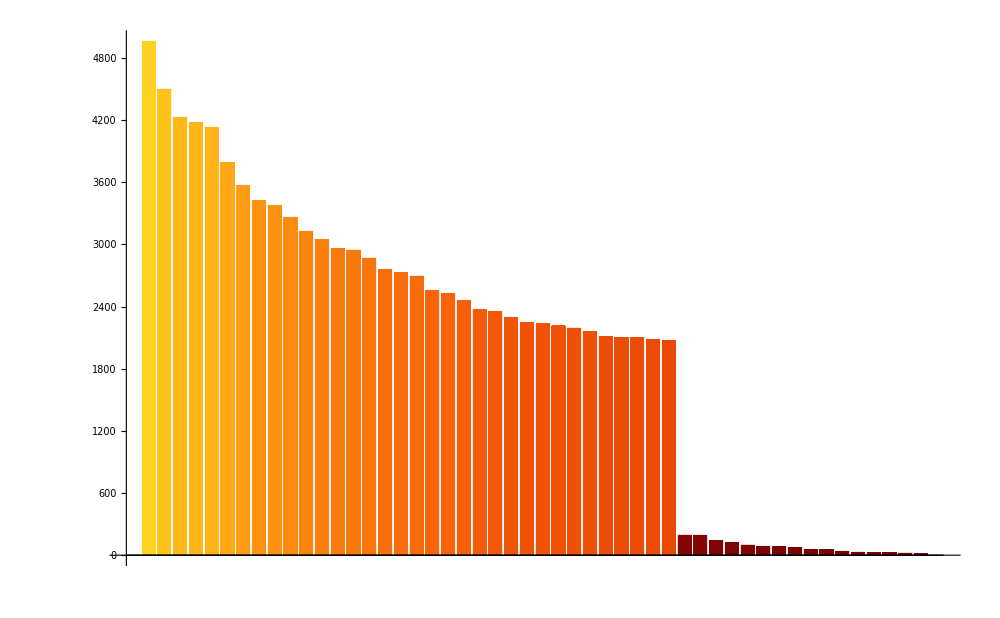

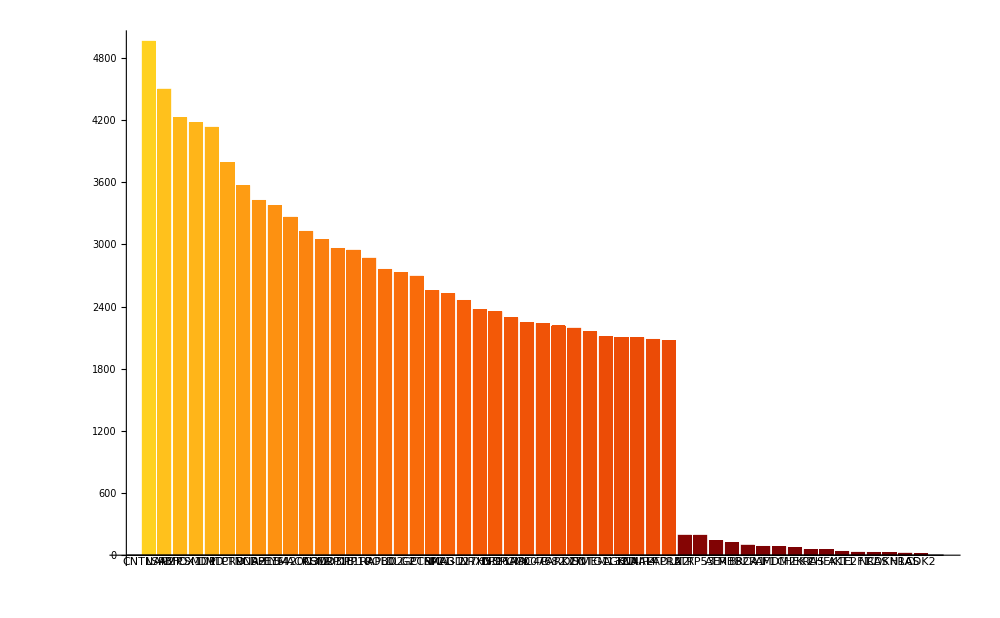

```mathematica
histTop50NoLabels = MutationHistogram[important50, Labeled->False]
histTop50 = MutationHistogram[important50]
```

```mathematica
If[export,
Export["./top50NoLabels.svg", histTop50NoLabels];
Export["./top50.svg", histTop50]
];
```

```mathematica
important100 = Join[MutationData[top84Mutated], (* Top 84 mutated genes *)
				    Map[GetMutations[dataset],mainGenes16] (* Main 16 genes *)
]
```

{{CNTNAP2,4963},{LSAMP,4501},{RBFOX1,4223},{CSMD1,4175},{DMD,4132},{PTPRD,3791},{CTNNA2,3567},{PCDH15,3425},{EYS,3375},{RP11-420N3.2,3263},{MACROD2,3126},{CSMD3,3046},{LRP1B,2961},{DPP10,2945},{IL1RAPL1,2868},{ROBO2,2759},{DLG2,2728},{GPC5,2694},{CTNNA3,2555},{MAGI2,2525},{RP11-127H5.1,2459},{NRXN3,2371},{DPP6,2350},{OPCML,2291},{LRRC4C,2243},{AC007682.1,2235},{PARK2,2213},{DCC,2192},{SNTG1,2156},{TMEM132D,2108},{AGBL4,2101},{KCNIP4,2099},{NAALADL2,2083},{PTPRN2,2072},{TM4SF2,2071},{PRKG1,2038},{RYR2,2017},{DAB1,2017},{CDH12,2008},{CCSER1,1996},{GRID2,1967},{CDH18,1943},{NRG1,1941},{NKAIN2,1930},{IL1RAPL2,1927},{RP11-32K4.1,1899},{SGCZ,1881},{CNTN5,1878},{GPC6,1869},{PDE4D,1838},{PTPRT,1799},{AUTS2,1741},{ASIC2,1719},{GRM8,1708},{NRXN1,1693},{RGS7,1690},{ERBB4,1678},{CDH13,1675},{GRM7,1673},{ANKS1B,1669},{TBC1D5,1665},{RP11-40F8.2,1663},{CNBD1,1656},{CNTN4,1654},{NRG3,1638},{CNTNAP5,1634},{NELL1,1627},{GALNTL6,1616},{SDK1,1607},{USH2A,1604},{NTM,1603},{RALYL,1583},{RIMS2,1577},{LRRTM4,1573},{CDH4,1569},{EPHA6,1552},{BAI3,1551},{CADM2,1548},{FHIT,1539},{LPHN3,1519},{ZNF385D,1516},{KHDRBS2,1509},{SPAG16,1508},{DIAPH2,1507},{CDK2,13},{TP53,193},{MDM2,83},{BRCA1,98},{ERBB2,119},{ATM,141},{AKT1,36},{CHEK1,51},{CHEK2,73},{E2F1,28},{ATR,194},{HRAS,20},{KRAS,54},{NRAS,26},{CDKN1A,25},{RAF1,84}}

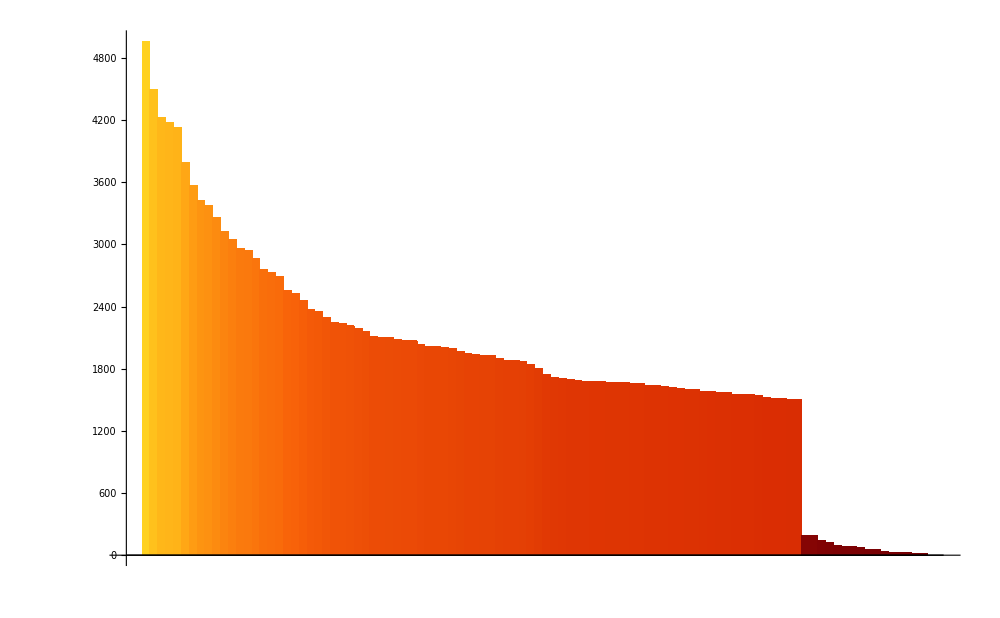

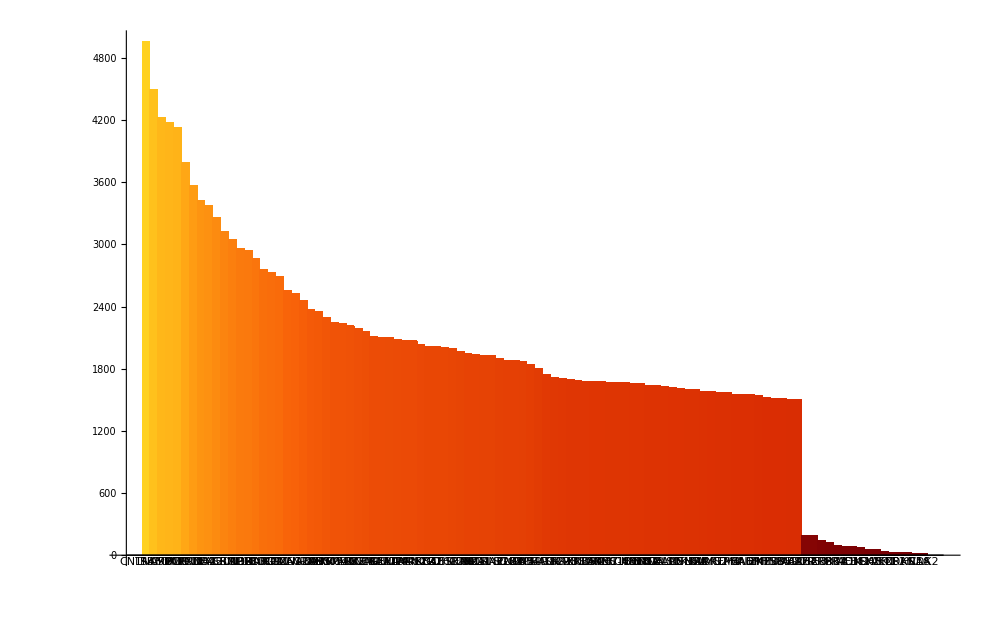

```mathematica
histTop100NoLabels = MutationHistogram[important100, Labeled->False]
histTop100 = MutationHistogram[important100]
```

```mathematica
If[export,
Export["./top100NoLabels.svg", histTop100NoLabels];
Export["./top100.svg", histTop100]
];
```